```mathematica
Quit[]
```

Script to import data from multiple raw files and export as a single data file.

```mathematica
files = FileNames["/path/NtoNdist-B*.m","/path/"];
```

```mathematica
consolidatedNtoN=Flatten[Join[Import[#]&/@files],1];
```

```mathematica
Export["/path/new/NtoN-workDist.m",consolidatedNtoN];
```

Import Data. For points where the system experienced an error, manually remove these points.

```mathematica
distributionNtoNplus4={{4.001, 1.3903406277223369*^-18}, {4.201, 1.419117106302333*^-10}, 
 {4.401, 1.4264474671163405*^-9}, {4.601, 5.326197961536723*^-9}, 
 {4.801, 1.3171761717667018*^-8}, {5.001, 2.6373258171489556*^-8}, 
 {5.201, 4.6602663988074196*^-8}, {5.401, 7.372603167102817*^-8}, 
 {5.601, 1.10356894833521*^-7}, {5.801, 1.5661020777666884*^-7}, 
 {6.001, 2.1479682180495807*^-7}, {6.201, 2.8212506907044265*^-7}, 
 {6.401, 3.6266539923994245*^-7}, {6.601, 4.585091566132856*^-7}, 
 {6.801, 5.720652322470452*^-7}, {7.001, 6.927675802274441*^-7}, 
 {7.201, 8.309166232788799*^-7}, {7.401, 9.98180976831818*^-7}, 
 {7.601, 1.1696695781086123*^-6}, {7.801, 1.3680476305704964*^-6}, 
 {8.001, 1.595225394918364*^-6}, {8.201, 1.8379683466436836*^-6}, 
 {8.401, 2.105929364182846*^-6}, {8.601, 2.3915979748784284*^-6}, 
 {8.801, 2.697660131216326*^-6}, {9.001, 3.0556391227814835*^-6}, 
 {9.201, 3.415968702471492*^-6}, {9.401, 3.831745792297726*^-6}, 
 {9.601, 4.2854847453810995*^-6}, {9.801, 4.753556748505417*^-6}, 
 {10.001, 5.2406575498037145*^-6}, {10.201, 5.77570744574458*^-6}, 
 {10.401, 6.483933257645332*^-6}, {10.601, 6.972990421002071*^-6}, 
 {10.801, 7.620617203949477*^-6}, {11.001, 8.376770460165743*^-6}, 
 {11.201, 9.102125851789624*^-6}, {11.401, 9.894350230421445*^-6}, 
 {11.601, 0.000010757724243372526}, {11.801, 0.000011589902168346676}, 
 {12.001, 0.000012529363568740545}, {12.201, 0.000013470759491373807}, 
 {12.401, 0.000014586701749560143}, {12.601, 0.00001568556098708672}, 
 {12.801, 0.000016869303842822553}, {13.001, 0.000018252056447571027}, 
 {13.201, 0.00001949698913113916}, {13.401, 0.000020797461438555715}, 
 {13.601, 0.000022186482128756973}, {13.801, 0.000023659359727134902}, 
 {14.001, 0.000025175787589791912}, {14.201, 0.000026900967833604123}, 
 {14.401, 0.000028602138730528572}, {14.601, 0.000030622468979995625}, 
 {14.801, 0.00003236433507592427}, {15.001, 0.000034545011151678304}, 
 {15.201, 0.00003634617652279809}, {15.401, 0.000038504706945978085}, 
 {15.601, 0.00004079072678934565}, {15.801, 0.00004304084116213844}, 
 {16.001, 0.00004526255631242916}, {16.201, 0.00004802758377015733}, 
 {16.401, 0.000050681312131331786}, {16.601, 0.000053194167306221976}, 
 {16.801, 0.00005630870160333782}, {17.001, 0.00005937374960031659}, 
 {17.201, 0.00006209976525496926}, {17.401, 0.00006538423236583031}, 
 {17.601, 0.00006850738064715982}, {17.801, 0.00007220195917991744}, 
 {18.001, 0.00007588856301939458}, {18.201, 0.00007963288898841133}, 
 {18.401, 0.00008320619439356174}, {18.601, 0.00008711823732491924}, 
 {18.801, 0.00009092274091795116}, {19.001, 0.00009527023808958182}, 
 {19.201, 0.0000994671386647113}, {19.401, 0.00010396590234736629}, 
 {19.601, 0.00010816990224319974}, {19.801, 0.00011321485197862314}, 
 {20.001, 0.0001187765608166202}, {20.201, 0.00012355306142423035}, 
 {20.401, 0.00012858977571351856}, {20.601, 0.0001339290660346374}, 
 {20.801, 0.00013987001804055955}, {21.001, 0.00014644621582892553}, 
 {21.201, 0.00015207879524712435}, {21.401, 0.00015822412301032466}, 
 {21.601, 0.0001645961319074566}, {21.801, 0.0001712607438504276}, 
 {22.001, 0.0001776446748366964}, {22.201, 0.00018433231830813327}, 
 {22.401, 0.00019110072025317924}, {22.601, 0.00019820688395233934}, 
 {22.801, 0.00020564297312379017}, {23.001, 0.00021346548208029138}, 
 {23.201, 0.00022195834340548305}, {23.401, 0.00023016278025477516}, 
 {23.601, 0.00023889490773614934}, {23.801, 0.0002469936846349804}, 
 {24.001, 0.00025495753073218297}, {24.201, 0.0002636845304743278}, 
 {24.401, 0.00027361288448477536}, {24.601, 0.00028315275281939125}, 
 {24.801, 0.0002930365921880108}, {25.001, 0.0003021220739818088}, 
 {25.201, 0.00031177720434882536}, {25.401, 0.00032342795061091203}, 
 {25.601, 0.00033379505680895436}, {25.801, 0.00034436881744161863}, 
 {26.001, 0.0003567850638021168}, {26.201, 0.0003665517509119313}, 
 {26.401, 0.0003807262302890616}, {26.601, 0.00039111207377558746}, 
 {26.801, 0.00040545043124226137}, {27.001, 0.0004160557573652334}, 
 {27.201, 0.0004302868168701552}, {27.401, 0.00044267210863099083}, 
 {27.601, 0.00045499010767503117}, {27.801, 0.00047039217615454514}, 
 {28.001, 0.0004869140186986368}, {28.201, 0.000500444494450397}, 
 {28.401, 0.0005173333641685968}, {28.601, 0.0005284559719935529}, 
 {28.801, 0.0005455954056442675}, {29.001, 0.0005630834496704303}, 
 {29.201, 0.0005767829202214048}, {29.401, 0.0005943669928017736}, 
 {29.601, 0.0006091982482537479}, {29.801, 0.0006257016083483798}, 
 {30.001, 0.0006455558157004743}};
```

```mathematica
distributionNtoNplus2tree={{0.001, 0.}, {0.201, 0.}, {0.401, 2.0429575347170123*^-15}, 
 {0.601, 1.3312601855536025*^-10}, {0.801, 1.683643456533081*^-9}, 
 {1.001, 8.479812023614677*^-9}, {1.201, 2.2811370064079168*^-8}, 
 {1.401, 5.157839993983894*^-8}, {1.601, 9.258753489659618*^-8}, 
 {1.801, 1.5364692821684642*^-7}, {2.001, 2.3602423681615903*^-7}, 
 {2.101, 2.8310285147340635*^-7}, {2.201, 3.303867287572434*^-7}, 
 {2.301, 3.852448644773713*^-7}, {2.401, 4.4137454256726246*^-7}, 
 {2.501, 5.019285391538037*^-7}, {2.601, 5.608799135591744*^-7}, 
 {2.701, 6.281705739812451*^-7}, {2.801, 6.934213613745491*^-7}, 
 {2.901, 7.596369016437272*^-7}, {3.001, 8.273022014330379*^-7}, 
 {3.101, 8.965484467555015*^-7}, {3.201, 9.659125171024104*^-7}, 
 {3.301, 1.0319385914921644*^-6}, {3.401, 1.1002681020758111*^-6}, 
 {3.501, 1.1680001683627917*^-6}, {3.601, 1.2496032717237028*^-6}, 
 {3.701, 1.3256072816235671*^-6}, {3.801, 1.3967889317295563*^-6}, 
 {3.901, 1.4861749484165916*^-6}, {4.001, 1.5424396865854226*^-6}, 
 {4.101, 1.6497365065803308*^-6}, {4.201, 1.6996012845605912*^-6}, 
 {4.301, 1.790873868481244*^-6}, {4.401, 1.855808974937691*^-6}, 
 {4.501, 1.934243380072678*^-6}, {4.601, 2.052969728774302*^-6}, 
 {4.701, 2.114510583568404*^-6}, {4.801, 2.190724645828408*^-6}, 
 {4.901, 2.2673927433534043*^-6}, {5.001, 2.368027829071641*^-6}, 
 {5.201, 2.555860441441743*^-6}, {5.401, 2.697776527928196*^-6}, 
 {5.601, 2.8876831647299216*^-6}, {5.801, 3.0642000854472516*^-6}, 
 {6.001, 3.281214301087169*^-6}, {6.201, 3.481598510561382*^-6}, 
 {6.401, 3.659259534417442*^-6}, {6.601, 3.85431920873876*^-6}, 
 {6.801, 4.049433006054026*^-6}, {7.001, 4.301215277752969*^-6}, 
 {7.201, 4.4583240803315925*^-6}, {7.401, 4.6858737608578606*^-6}, 
 {7.601, 4.9074926460912*^-6}, {7.801, 5.143814012492505*^-6}, 
 {8.001, 5.341216696166832*^-6}, {8.201, 5.57086197975072*^-6}, 
 {8.401, 5.838493889981659*^-6}, {8.601, 6.072222162653258*^-6}, 
 {8.801, 6.290956410473661*^-6}, {9.001, 6.579220004936043*^-6}, 
 {9.201, 6.936915139298318*^-6}, {9.401, 7.060269762302033*^-6}, 
 {9.601, 7.336962992028529*^-6}, {9.801, 7.567166592110528*^-6}, 
 {10.001, 7.991078310351351*^-6}, {10.334, 8.367328395488306*^-6}, 
 {10.667, 8.804617078829028*^-6}, {11.001, 9.286092940149843*^-6}, 
 {11.334, 9.775944615332884*^-6}, {11.667, 0.00001028676200107149}, 
 {12.001, 0.000010826131602587386}, {12.334, 0.000011413850383449172}, 
 {12.667, 0.000011848906060727034}, {13.001, 0.0000124264788260527}, 
 {13.334, 0.000013043994345287254}, {13.667, 0.000013626779547343582}, 
 {14.001, 0.000014305616204369309}, {14.334, 0.000014920275033250909}, 
 {14.667, 0.00001553359028584169}, {15.001, 0.000016111978973324964}, 
 {15.334, 0.000016769932406289885}, {15.667, 0.00001739294117198457}, 
 {16.001, 0.000018067580381035916}, {16.334, 0.000018726805978721924}, 
 {16.667, 0.0000194465934138721}, {17.001, 0.000020179285759447346}, 
 {17.334, 0.000020931362501135805}, {17.667, 0.000021675272214621495}, 
 {18.001, 0.00002234177676574242}, {18.334, 0.000023208086722084973}, 
 {18.667, 0.000024080698064684937}, {19.001, 0.000024839145100729924}, 
 {19.334, 0.00002561598032896051}, {19.667, 0.00002653762250586585}, 
 {20.001, 0.00002722346057208683}, {20.334, 0.000028063155562696553}, 
 {20.667, 0.000028856078022013806}, {21.001, 0.000029723018848788876}, 
 {21.334, 0.00003059016733222218}, {21.667, 0.000031467961024755586}, 
 {22.001, 0.00003251423845503418}, {22.334, 0.00003357072664917487}, 
 {22.667, 0.000034669221046273675}, {23.001, 0.00003561785898596736}, 
 {23.334, 0.00003671724772701981}, {23.667, 0.00003751564143872055}, 
 {24.001, 0.000038440780133366074}, {24.334, 0.00003972378679626001}, 
 {24.667, 0.00004055340097812591}, {25.001, 0.00004138655887159184}, 
 {25.334, 0.00004262945738970023}, {25.667, 0.000043874361437096595}, 
 {26.001, 0.00004487071551419092}, {26.334, 0.000045907314867067104}, 
 {26.667, 0.00004704226048244001}, {27.001, 0.00004825667044084739}, 
 {27.334, 0.00004937044757074761}, {27.667, 0.000050616837429120065}, 
 {28.001, 0.00005184471916989388}, {28.334, 0.00005297617117662631}, 
 {28.667, 0.00005433395391396441}, {29.001, 0.00005569863558276066}, 
 {29.334, 0.000057083789164312297}, {29.667, 0.00005847019496762527}, 
 {30.001, 0.00005988509999641279}};
```

```mathematica
distributionNtoN = {{-30.001, 5.218908913253999*^-20}, {-29.501, 8.285496255968258*^-20}, 
 {-29.001, 1.4093319375315389*^-19}, {-28.501, 2.192980960697638*^-19}, 
 {-28.001, 3.3542044042234274*^-19}, {-27.501, 5.944260817635321*^-19}, 
 {-27.001, 9.498062443399195*^-19}, {-26.501, 1.6296211444393988*^-18}, 
 {-26.001, 2.540781634123496*^-18}, {-25.501, 3.940532935290128*^-18}, 
 {-25.001, 6.403863696547505*^-18}, {-24.501, 1.0500445117151286*^-17}, 
 {-24.001, 1.8796049136461686*^-17}, {-23.501, 3.379300512405913*^-17}, 
 {-23.001, 5.238265947873117*^-17}, {-22.501, 8.101300099813168*^-17}, 
 {-22.001, 1.4192984881131705*^-16}, {-21.501, 2.2049804958207243*^-16}, 
 {-21.001, 3.7831170275746696*^-16}, {-20.501, 7.263715238915239*^-16}, 
 {-20.001, 9.77574524180941*^-16}, {-19.501, 1.5954586515018341*^-15}, 
 {-19.001, 2.495648247905194*^-15}, {-18.501, 4.721156773726007*^-15}, 
 {-18.001, 7.157174152896437*^-15}, {-17.501, 1.2262267536065253*^-14}, 
 {-17.001, 2.1680282370782105*^-14}, {-16.501, 3.4553512573126204*^-14}, 
 {-16.001, 5.411882106748955*^-14}, {-15.501, 8.430867517908973*^-14}, 
 {-15.001, 1.4688957391274982*^-13}, {-14.501, 2.3743456958438814*^-13}, 
 {-14.001, 3.977553392227788*^-13}, {-13.501, 6.484035502966478*^-13}, 
 {-13.001, 1.0982246276865806*^-12}, {-12.501, 1.7292669525443938*^-12}, 
 {-12.001, 2.9089842337932466*^-12}, {-11.501, 4.858696190108045*^-12}, 
 {-11.001, 7.643801824712938*^-12}, {-10.501, 1.2789984288779118*^-11}, 
 {-10.001, 2.177510612358411*^-11}, {-9.667, 2.942060220217925*^-11}, 
 {-9.334, 4.118643545429913*^-11}, {-9.001, 5.7701123253378353*^-11}, 
 {-8.667, 7.989721300548185*^-11}, {-8.334, 1.1123674389522916*^-10}, 
 {-8.001, 1.5421439694522806*^-10}, {-7.667, 2.191312551567535*^-10}, 
 {-7.334, 3.087504385946419*^-10}, {-7.001, 4.200564905074156*^-10}, 
 {-6.801, 5.36788281797453*^-10}, {-6.601, 6.287944029307953*^-10}, 
 {-6.401, 7.766271314145202*^-10}, {-6.201, 9.509703563596447*^-10}, 
 {-6.001, 1.1572471405608233*^-9}, {-5.801, 1.4225851874890126*^-9}, 
 {-5.601, 1.741134101118063*^-9}, {-5.401, 2.168036161331995*^-9}, 
 {-5.201, 2.5859756030363323*^-9}, {-5.001, 3.192704043234979*^-9}, 
 {-4.901, 3.6404235542714697*^-9}, {-4.801, 4.0333200253433266*^-9}, 
 {-4.701, 4.255620251812632*^-9}, {-4.601, 4.782505345977291*^-9}, 
 {-4.501, 5.28650798968088*^-9}, {-4.401, 5.745250335393039*^-9}, 
 {-4.301, 6.495858384722157*^-9}, {-4.201, 7.053195737907041*^-9}, 
 {-4.101, 7.882611388055044*^-9}, {-4.001, 8.651853302682148*^-9}, 
 {-3.901, 9.80066863809811*^-9}, {-3.801, 1.0551683745161422*^-8}, 
 {-3.701, 1.1674889527679056*^-8}, {-3.601, 1.3050789047076186*^-8}, 
 {-3.501, 1.440073114112443*^-8}, {-3.401, 1.5756640686536656*^-8}, 
 {-3.301, 1.7727695596763243*^-8}, {-3.201, 1.9501058603976548*^-8}, 
 {-3.101, 2.1541107453031358*^-8}, {-3.001, 2.439774895631149*^-8}, 
 {-2.901, 2.6488058464788684*^-8}, {-2.801, 2.9058222439957088*^-8}, 
 {-2.701, 3.2543222870399834*^-8}, {-2.601, 3.601124384278356*^-8}, 
 {-2.501, 3.976045908237993*^-8}, {-2.401, 4.416617523183444*^-8}, 
 {-2.301, 4.878175602284064*^-8}, {-2.001, 6.51954506057978*^-8}, 
 {-1.901, 7.221517986710426*^-8}, {-1.801, 8.006015983271658*^-8}, 
 {-1.701, 8.955294526135471*^-8}, {-1.601, 9.857127244358876*^-8}, 
 {-1.501, 1.0995560795377873*^-7}, {-1.401, 1.207353529048004*^-7}, 
 {-2.201, 5.388132372925336*^-8}, {-2.101, 6.01187211351992*^-8}, 
 {-1.301, 1.3370742547866224*^-7}, {-1.201, 1.484369146116848*^-7}, 
 {-1.101, 1.6509735468223602*^-7}, {-1.001, 1.8148724202914878*^-7}, 
 {-0.901, 2.0053495368092256*^-7}, {-0.801, 2.222251756439537*^-7}, 
 {-0.701, 2.450567961661131*^-7}, {-0.601, 2.6904028549475206*^-7}, 
 {-0.501, 2.9721919255582714*^-7}, {-0.401, 3.241151925631456*^-7}, 
 {-0.301, 3.553837548964379*^-7}, {-0.201, 3.861443554956208*^-7}, 
 {-0.101, 4.1712943375999696*^-7}, {-0.001, 4.390436058070449*^-7}, 
 {0.001, 4.3930566901431676*^-7}, {0.101, 4.634283755333585*^-7}, 
 {0.201, 4.7569423553896156*^-7}, {0.301, 4.846938979984902*^-7}, 
 {0.401, 4.902126343603897*^-7}, {0.501, 4.945433753937096*^-7}, 
 {0.601, 4.973322959138864*^-7}, {0.701, 4.991873577653967*^-7}, 
 {0.801, 5.003145547479106*^-7}, {0.901, 5.008897750102333*^-7}, 
 {1.001, 5.010446532135909*^-7}, {1.101, 5.00884049138357*^-7}, 
 {1.201, 5.004836939488097*^-7}, {1.301, 4.999056643630178*^-7}, 
 {1.401, 4.991956878515806*^-7}, {1.501, 4.983905446751653*^-7}, 
 {1.601, 4.975188492577093*^-7}, {1.701, 4.966025147321088*^-7}, 
 {1.801, 4.956593524556011*^-7}, {1.901, 4.947035051722557*^-7}, 
 {2.001, 4.93744925314831*^-7}, {2.101, 4.927926101675113*^-7}, 
 {2.201, 4.918533368338435*^-7}, {2.301, 4.909317245966636*^-7}, 
 {2.401, 4.90031867341313*^-7}, {2.501, 4.891573400854836*^-7}, 
 {2.601, 4.883079465760341*^-7}, {2.701, 4.874876307757933*^-7}, 
 {2.801, 4.866968807483608*^-7}, {2.901, 4.859356278863007*^-7}, 
 {3.001, 4.852047414807025*^-7}, {3.101, 4.845038669480714*^-7}, 
 {3.201, 4.83832845168985*^-7}, {3.301, 4.831912857634679*^-7}, 
 {3.401, 4.825785174544743*^-7}, {3.501, 4.819947965140368*^-7}, 
 {3.601, 4.814379346517299*^-7}, {3.701, 4.8090862209511*^-7}, 
 {3.801, 4.804054422231604*^-7}, {3.901, 4.799272222724698*^-7}, 
 {4.001, 4.794735206001586*^-7}, {4.101, 4.790433346352083*^-7}, 
 {4.201, 4.786360926670574*^-7}, {4.301, 4.782503573336885*^-7}, 
 {4.401, 4.778858793650119*^-7}, {4.501, 4.775413830585956*^-7}, 
 {4.601, 4.772162785091431*^-7}, {4.701, 4.769114023931714*^-7}, 
 {4.801, 4.766217819470255*^-7}, {4.901, 4.7634894185031623*^-7}, 
 {5.001, 4.760932178007456*^-7}, {5.201, 4.756275658230887*^-7}, 
 {5.401, 4.752182345201567*^-7}, {5.601, 4.748602618178223*^-7}, 
 {5.801, 4.7454857399357985*^-7}, {6.001, 4.74279059040506*^-7}, 
 {6.201, 4.740476005393142*^-7}, {6.401, 4.7385032662022197*^-7}, 
 {6.601, 4.736841736296306*^-7}, {6.801, 4.735450918597169*^-7}, 
 {7.001, 4.734311393993999*^-7}, {7.334, 4.7328950521954774*^-7}, 
 {7.667, 4.7319892765727724*^-7}, {8.001, 4.731502069158719*^-7}, 
 {8.334, 4.7313595480543643*^-7}, {8.667, 4.731539797186439*^-7}, 
 {9.001, 4.7318540871510194*^-7}, {9.334, 4.73238922587333*^-7}, 
 {9.667, 4.733064363100252*^-7}, {10.001, 4.733844707475857*^-7}, 
 {10.501, 4.7351561875623854*^-7}, {11.001, 4.7365771692904193*^-7}, 
 {11.501, 4.738053299165207*^-7}, {12.001, 4.739563654471181*^-7}, 
 {12.501, 4.7410257343628614*^-7}, {13.001, 4.7424768321373337*^-7}, 
 {13.501, 4.7438887644231754*^-7}, {14.001, 4.7452296275939933*^-7}, 
 {14.501, 4.746520676351052*^-7}, {15.001, 4.747745566165174*^-7}, 
 {15.501, 4.748908833086563*^-7}, {16.001, 4.750008020001066*^-7}, 
 {16.501, 4.7510437811191694*^-7}, {17.001, 4.7520427092303695*^-7}, 
 {17.501, 4.752934437765302*^-7}, {18.001, 4.7538086198227056*^-7}, 
 {18.501, 4.7545964050347905*^-7}, {19.001, 4.755346325426951*^-7}, 
 {19.501, 4.7560456679666444*^-7}, {20.001, 4.7566948427922023*^-7}, 
 {20.501, 4.7572963195606543*^-7}, {21.001, 4.7578512712799436*^-7}, 
 {21.501, 4.758355861822899*^-7}, {22.001, 4.758816297939184*^-7}, 
 {22.501, 4.7592303509140474*^-7}, {23.001, 4.7596017460183277*^-7}, 
 {23.501, 4.7599196360108474*^-7}, {24.001, 4.7602152502726347*^-7}, 
 {24.501, 4.7604186273182217*^-7}, {25.001, 4.7606077283206554*^-7}, 
 {25.501, 4.760720191140482*^-7}, {26.001, 4.760792508440966*^-7}, 
 {26.501, 4.760810303745723*^-7}, {27.001, 4.760770222376327*^-7}, 
 {27.501, 4.7606726599189896*^-7}, {28.001, 4.7605126990973*^-7}, 
 {28.501, 4.7602884772356874*^-7}, {29.001, 4.7599971013393*^-7}, 
 {29.501, 4.759635449819495*^-7}, {30.001, 4.7592007955847737*^-7}};
```

```mathematica
distributionNtoNminus2tree ={{-0.001, 0.}, {-0.201, 0.}, {-0.401, 1.3680671033879484*^-15}, 
 {-0.601, 7.298810029949669*^-11}, {-0.801, 7.557599610072241*^-10}, 
 {-1.001, 3.1163986801844568*^-9}, {-1.201, 6.863777351452499*^-9}, 
 {-1.401, 1.2706345325176497*^-8}, {-1.601, 1.8674423127311482*^-8}, 
 {-1.801, 2.537227100294943*^-8}, {-2.001, 3.191057553904263*^-8}, 
 {-2.101, 3.4633117611401574*^-8}, {-2.201, 3.657128505226598*^-8}, 
 {-2.301, 3.8585645884154585*^-8}, {-2.401, 4.000056351952782*^-8}, 
 {-2.501, 4.1159605146858356*^-8}, {-2.601, 4.16169219706955*^-8}, 
 {-2.701, 4.217433565179975*^-8}, {-2.801, 4.212484834870164*^-8}, 
 {-2.901, 4.175588919276494*^-8}, {-3.001, 4.1147780119299695*^-8}, 
 {-3.101, 4.034843082871154*^-8}, {-3.201, 3.93333754418016*^-8}, 
 {-3.301, 3.80231279714247*^-8}, {-3.401, 3.668284384870903*^-8}, 
 {-3.501, 3.523529506711758*^-8}, {-3.601, 3.410968946486697*^-8}, 
 {-3.701, 3.274091780655166*^-8}, {-3.801, 3.121602708838126*^-8}, 
 {-3.901, 3.005292106864648*^-8}, {-4.001, 2.8222523150989943*^-8}, 
 {-4.101, 2.7313223752503342*^-8}, {-4.201, 2.546102877137182*^-8}, 
 {-4.301, 2.427529893541183*^-8}, {-4.401, 2.276162780384964*^-8}, 
 {-4.501, 2.1466030223923226*^-8}, {-4.601, 2.0615479808853807*^-8}, 
 {-4.701, 1.921283642315973*^-8}, {-4.801, 1.801108896186733*^-8}, 
 {-4.901, 1.6867450478536987*^-8}, {-5.001, 1.593969189034763*^-8}, 
 {-5.201, 1.4085478340666782*^-8}, {-5.401, 1.2172547757646575*^-8}, 
 {-5.601, 1.0667590409856416*^-8}, {-5.801, 9.267760820196543*^-9}, 
 {-6.001, 8.125190572870289*^-9}, {-6.201, 7.058600562229461*^-9}, 
 {-6.401, 6.0739921698757475*^-9}, {-6.601, 5.2380523877587415*^-9}, 
 {-6.801, 4.505630899302522*^-9}, {-7.001, 3.918269267865478*^-9}, 
 {-7.201, 3.325194449125952*^-9}, {-7.401, 2.8613917737562305*^-9}, 
 {-7.601, 2.453507530599445*^-9}, {-7.801, 2.1054939958435295*^-9}, 
 {-8.001, 1.7899876530853448*^-9}, {-8.201, 1.5285278442193308*^-9}, 
 {-8.401, 1.311574283633285*^-9}, {-8.601, 1.1168139000992588*^-9}, 
 {-8.801, 9.47307469268317*^-10}, {-9.001, 8.111287632459112*^-10}, 
 {-9.201, 7.002015679335655*^-10}, {-9.401, 5.83470480540889*^-10}, 
 {-9.601, 4.964265550257957*^-10}, {-9.801, 4.1919209845007806*^-10}, 
 {-10.001, 3.624318115527198*^-10}, {-10.334, 2.7201169110388866*^-10}, 
 {-10.667, 2.051593182660063*^-10}, {-11.001, 1.5493857762669344*^-10}, 
 {-11.334, 1.1691360980496192*^-10}, {-11.667, 8.817897612699063*^-11}, 
 {-12.001, 6.645157233261844*^-11}, {-12.334, 5.021622548141986*^-11}, 
 {-12.667, 3.736543648360996*^-11}, {-13.001, 2.805986044334478*^-11}, 
 {-13.334, 2.1111932178018185*^-11}, {-13.667, 1.5808495573128352*^-11}, 
 {-14.001, 1.1883641574037609*^-11}, {-14.334, 8.883820248835027*^-12}, 
 {-14.667, 6.62940711152234*^-12}, {-15.001, 4.923765690773678*^-12}, 
 {-15.334, 3.673327627406439*^-12}, {-15.667, 2.730746183330724*^-12}, 
 {-16.001, 2.031206047573653*^-12}, {-16.334, 1.5090290943426727*^-12}, 
 {-16.667, 1.1232007364136226*^-12}, {-17.001, 8.345748563624089*^-13}, 
 {-17.334, 6.204930971234552*^-13}, {-17.667, 4.605576633530389*^-13}, 
 {-18.001, 3.3992470141819194*^-13}, {-18.334, 2.530953924807719*^-13}, 
 {-18.667, 1.882322168833778*^-13}, {-19.001, 1.390295608516267*^-13}, 
 {-19.334, 1.0276884399388572*^-13}, {-19.667, 7.631192601927149*^-14}, 
 {-20.001, 5.605565138464039*^-14}, {-20.334, 4.1418318306102746*^-14}, 
 {-20.667, 3.052623646765769*^-14}, {-21.001, 2.251513387767876*^-14}, 
 {-21.334, 1.660899820919122*^-14}, {-21.667, 1.224644550859402*^-14}, 
 {-22.001, 9.060677844902937*^-15}, {-22.334, 6.705447455743505*^-15}, 
 {-22.667, 4.9635350455666935*^-15}, {-23.001, 3.651408596620639*^-15}, 
 {-23.334, 2.698004754090958*^-15}, {-23.667, 1.9758996866074947*^-15}, 
 {-24.001, 1.4497408079037509*^-15}, {-24.334, 1.07381311222701*^-15}, 
 {-24.667, 7.85751603003804*^-16}, {-25.001, 5.741998078267838*^-16}, 
 {-25.334, 4.2392921694100494*^-16}, {-25.667, 3.1273345683668125*^-16}, 
 {-26.001, 2.290193315422733*^-16}, {-26.334, 1.6794652717033005*^-16}, 
 {-26.667, 1.2335511990528952*^-16}, {-27.001, 9.060914862637283*^-17}, 
 {-27.334, 6.644491278174174*^-17}, {-27.667, 4.8828063646346956*^-17}, 
 {-28.001, 3.581168692659938*^-17}, {-28.334, 2.6228933204738533*^-17}, 
 {-28.667, 1.9281971316308885*^-17}, {-29.001, 1.4153710337525438*^-17}, 
 {-29.334, 1.039725012756913*^-17}, {-29.667, 7.633436700636946*^-18}, 
 {-30.001, 5.59822131729734*^-18}};
```

```mathematica
distributionNtoNminus4 ={{-4.001, 2.5556645245574994*^-20}, {-4.201, 2.125983440583366*^-12}, 
 {-4.401, 1.7495878859787788*^-11}, {-4.601, 5.348456340469972*^-11}, 
 {-4.801, 1.0829195791837175*^-10}, {-5.001, 1.7752410426993702*^-10}, 
 {-5.201, 2.568295963887686*^-10}, {-5.401, 3.326621987266674*^-10}, 
 {-5.601, 4.0767697872330444*^-10}, {-5.801, 4.736720652702972*^-10}, 
 {-6.001, 5.318958509172935*^-10}, {-6.201, 5.719811090603365*^-10}, 
 {-6.401, 6.020058185354682*^-10}, {-6.601, 6.231177871526251*^-10}, 
 {-6.801, 6.365154552524912*^-10}, {-7.001, 6.310907620571173*^-10}, 
 {-7.201, 6.197304030322777*^-10}, {-7.401, 6.095310493120691*^-10}, 
 {-7.601, 5.84777802396787*^-10}, {-7.801, 5.599767905083812*^-10}, 
 {-8.001, 5.346106852432461*^-10}, {-8.201, 5.043001160876087*^-10}, 
 {-8.401, 4.730829630646685*^-10}, {-8.601, 4.398817233447474*^-10}, 
 {-8.801, 4.0624028147333445*^-10}, {-9.001, 3.7671898978963103*^-10}, 
 {-9.201, 3.448023091861721*^-10}, {-9.401, 3.166607582209256*^-10}, 
 {-9.601, 2.89960435510888*^-10}, {-9.801, 2.633289207601554*^-10}, 
 {-10.001, 2.376875923695311*^-10}, {-10.201, 2.144703497936223*^-10}, 
 {-10.401, 1.9712502398249814*^-10}, {-10.601, 1.7356544037494461*^-10}, 
 {-10.801, 1.5530145734608462*^-10}, {-11.001, 1.3976647786595145*^-10}, 
 {-11.201, 1.243398224467076*^-10}, {-11.401, 1.1066130509315143*^-10}, 
 {-11.601, 9.850770309623669*^-11}, {-11.801, 8.689016063465678*^-11}, 
 {-12.001, 7.69061273220846*^-11}, {-12.201, 6.769631806776665*^-11}, 
 {-12.401, 6.001657192820754*^-11}, {-12.601, 5.2839094838113287*^-11}, 
 {-12.801, 4.652576098561673*^-11}, {-13.001, 4.1214864887350935*^-11}, 
 {-13.201, 3.604508541749892*^-11}, {-13.401, 3.148038920661277*^-11}, 
 {-13.601, 2.7494709837715883*^-11}, {-13.801, 2.4005171989759124*^-11}, 
 {-14.001, 2.0914056653740333*^-11}, {-14.201, 1.829583430070839*^-11}, 
 {-14.401, 1.5926621809440986*^-11}, {-14.601, 1.396067684796203*^-11}, 
 {-14.801, 1.208020239923169*^-11}, {-15.001, 1.0556837997705865*^-11}, 
 {-15.201, 9.093871098732182*^-12}, {-15.401, 7.887592148677746*^-12}, 
 {-15.601, 6.8412148937652215*^-12}, {-15.801, 5.910212637909904*^-12}, 
 {-16.001, 5.088538459651798*^-12}, {-16.201, 4.420648743026902*^-12}, 
 {-16.401, 3.819303663705284*^-12}, {-16.601, 3.2820209524634997*^-12}, 
 {-16.801, 2.844421059629421*^-12}, {-17.001, 2.4555798319019258*^-12}, 
 {-17.201, 2.1027644244166215*^-12}, {-17.401, 1.8126534977067126*^-12}, 
 {-17.601, 1.5549634155554638*^-12}, {-17.801, 1.341753547932408*^-12}, 
 {-18.001, 1.1546239902583901*^-12}, {-18.201, 9.919701059990173*^-13}, 
 {-18.401, 8.485997480115214*^-13}, {-18.601, 7.274403019867653*^-13}, 
 {-18.801, 6.215875795242166*^-13}, {-19.001, 5.332473730946773*^-13}, 
 {-19.201, 4.55817843722832*^-13}, {-19.401, 3.900707118903517*^-13}, 
 {-19.601, 3.3227700204743035*^-13}, {-19.801, 2.8473336618529007*^-13}, 
 {-20.001, 2.4457202919717743*^-13}, {-20.201, 2.0829108183587398*^-13}, 
 {-20.401, 1.7748632081702747*^-13}, {-20.601, 1.513471428140268*^-13}, 
 {-20.801, 1.294091730429589*^-13}, {-21.001, 1.1093273128913962*^-13}, 
 {-21.201, 9.431728187116646*^-14}, {-21.401, 8.03408760982207*^-14}, 
 {-21.601, 6.84265383628803*^-14}, {-21.801, 5.829131215487293*^-14}, 
 {-22.001, 4.9503893015554655*^-14}, {-22.201, 4.2056170476824905*^-14}, 
 {-22.401, 3.569695587604876*^-14}, {-22.601, 3.031301644076147*^-14}, 
 {-22.801, 2.5749304870432486*^-14}, {-23.001, 2.188367663639904*^-14}, 
 {-23.201, 1.8629686204561318*^-14}, {-23.401, 1.581648325176734*^-14}, 
 {-23.601, 1.3440729045451564*^-14}, {-23.801, 1.1377396479573988*^-14}, 
 {-24.001, 9.615368655605224*^-15}, {-24.201, 8.141864273540606*^-15}, 
 {-24.401, 6.916985389561423*^-15}, {-24.601, 5.860601525137041*^-15}, 
 {-24.801, 4.965745207930326*^-15}, {-25.001, 4.191660287521025*^-15}, 
 {-25.201, 3.541514624753742*^-15}, {-25.401, 3.0079003676917573*^-15}, 
 {-25.601, 2.5415983186580336*^-15}, {-25.801, 2.1468012755454806*^-15}, 
 {-26.001, 1.8210248510724407*^-15}, {-26.201, 1.531742129374604*^-15}, 
 {-26.401, 1.30257936130093*^-15}, {-26.601, 1.0955537666978142*^-15}, 
 {-26.801, 9.298466128384544*^-16}, {-27.001, 7.81207192396408*^-16}, 
 {-27.201, 6.614755476193759*^-16}, {-27.401, 5.57159007483361*^-16}, 
 {-27.601, 4.688565314596486*^-16}, {-27.801, 3.9686164950130955*^-16}, 
 {-28.001, 3.3633532633002453*^-16}, {-28.201, 2.830200928059255*^-16}, 
 {-28.401, 2.395371432115369*^-16}, {-28.601, 2.003329264875521*^-16}, 
 {-28.801, 1.693383041429166*^-16}, {-29.001, 1.4308649169887676*^-16}, 
 {-29.201, 1.1999946217548659*^-16}, {-29.401, 1.0124244504878685*^-16}, 
 {-29.601, 8.495867932229974*^-17}, {-29.801, 7.144261236887456*^-17}, 
 {-30.001, 6.034830027683055*^-17}} ;
```

Analytic expressions for the loop contributions.

```mathematica
analyticNtoNplus2loop[W_,β_] := Abs[1/2(1+1/(Exp[(β W)/2]-1))^2*1/(2(2 Pi)^4)Sqrt[1-(2/W)^2]HeavisideTheta[W-2]*(NIntegrate[q^2/(2Sqrt[1+q^2](Exp[β Sqrt[1+q^2]]-1)),{q,0,Infinity},AccuracyGoal->30])^2]
```

```mathematica
analyticNtoNminus2loop[W_,β_] := Abs[1/2(1/(Exp[(-β W)/2]-1))^2*1/(2(2 Pi)^4)Sqrt[1-(2/-W)^2]HeavisideTheta[-W-2]*(NIntegrate[q^2/(2Sqrt[1+q^2](Exp[β Sqrt[1+q^2]]-1)),{q,0,Infinity},AccuracyGoal->30])^2]
```

Define driving protocol and Fourier transform.

```mathematica
Lambda[t_]:=Piecewise[{{Exp[-t^2/(1-t^2)],Abs[t]<1}},0]
```

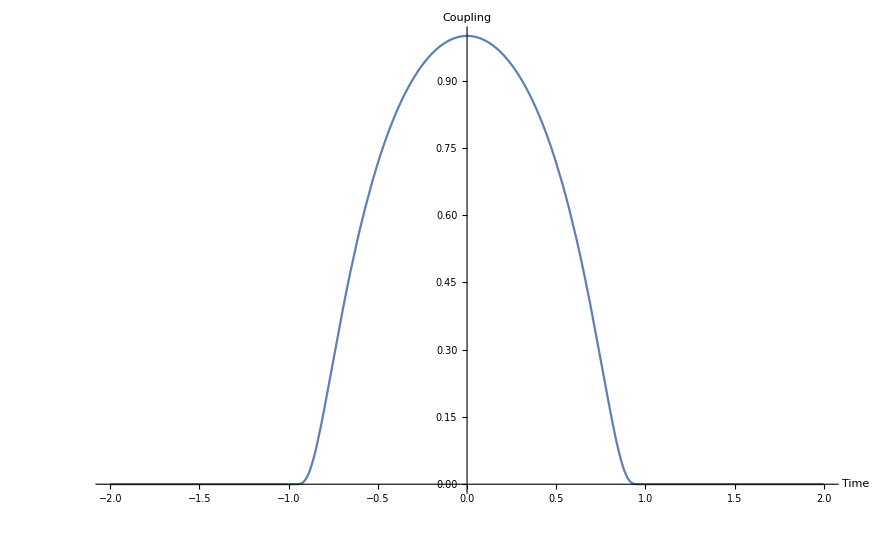

```mathematica
Plot[Lambda[t],{t,-2,2},AxesLabel->{Style["Time",Large],Style["Coupling",Large]},TicksStyle->Directive[Large],PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
FourierWork[W_]:=NIntegrate[Lambda[t]Exp[I t W],{t,-Infinity,Infinity},AccuracyGoal->20]
```

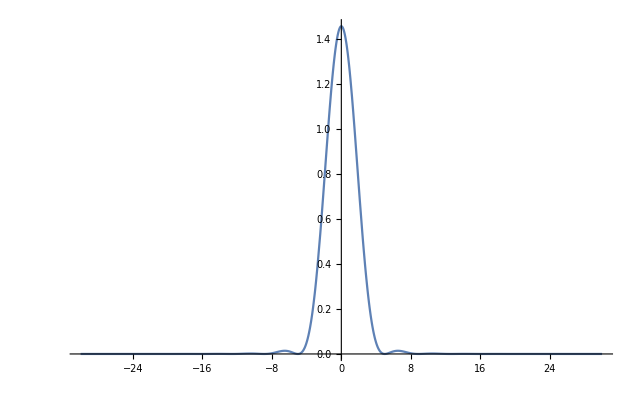

```mathematica
Plot[Abs[FourierWork[W]]^2,{W,-30,30},PlotRange->All]
```

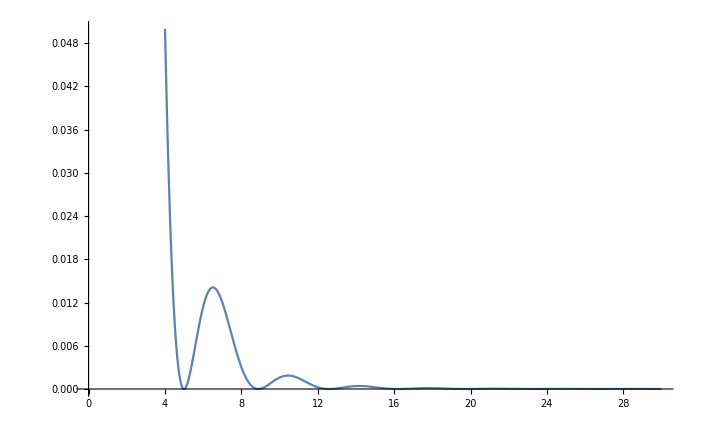

```mathematica
Plot[Abs[FourierWork[W]]^2,{W,0,30},PlotRange->{0,.05}]
```

Create unnormalized work distributions by multiplying by the Fourier transformed driving force.

```mathematica
unnormedNtoN=Table[0,{i,Length[distributionNtoN]},{j,2}];Do[unnormedNtoN[[i,1]]=distributionNtoN[[i,1]];unnormedNtoN[[i,2]]=Abs[FourierWork[distributionNtoN[[i,1]]]]^2*distributionNtoN[[i,2]];,{i,Length[distributionNtoN]}]
```

```mathematica
unnormedNtoNplus4=Table[0,{i,Length[distributionNtoNplus4]},{j,2}];Do[unnormedNtoNplus4[[i,1]]=distributionNtoNplus4[[i,1]];unnormedNtoNplus4[[i,2]]=Abs[FourierWork[distributionNtoNplus4[[i,1]]]]^2*distributionNtoNplus4[[i,2]];,{i,Length[distributionNtoNplus4]}]
```

```mathematica
unnormedNtoNplus2tree=Table[0,{i,Length[distributionNtoNplus2tree]},{j,2}];Do[unnormedNtoNplus2tree[[i,1]]=distributionNtoNplus2tree[[i,1]];unnormedNtoNplus2tree[[i,2]]=Abs[FourierWork[distributionNtoNplus2tree[[i,1]]]]^2*distributionNtoNplus2tree[[i,2]];,{i,Length[distributionNtoNplus2tree]}]
```

```mathematica
unnormedNtoNplus2loop=Table[0,{i,Length[distributionNtoNplus2tree]},{j,2}];Do[unnormedNtoNplus2loop[[i,1]]=distributionNtoNplus2tree[[i,1]];unnormedNtoNplus2loop[[i,2]]=Abs[FourierWork[distributionNtoNplus2tree[[i,1]]]]^2*analyticNtoNplus2loop[distributionNtoNplus2tree[[i,1]],1];,{i,Length[distributionNtoNplus2tree]}]
```

```mathematica
unnormedNtoNminus2tree=Table[0,{i,Length[distributionNtoNminus2tree]},{j,2}];Do[unnormedNtoNminus2tree[[i,1]]=distributionNtoNminus2tree[[i,1]];unnormedNtoNminus2tree[[i,2]]=Abs[FourierWork[distributionNtoNminus2tree[[i,1]]]]^2*distributionNtoNminus2tree[[i,2]];,{i,Length[distributionNtoNminus2tree]}]
```

```mathematica
unnormedNtoNminus2loop=Table[0,{i,Length[distributionNtoNminus2tree]},{j,2}];Do[unnormedNtoNminus2loop[[i,1]]=distributionNtoNminus2tree[[i,1]];unnormedNtoNminus2loop[[i,2]]=Abs[FourierWork[distributionNtoNminus2tree[[i,1]]]]^2*analyticNtoNminus2loop[distributionNtoNminus2tree[[i,1]],1];,{i,Length[distributionNtoNminus2tree]}]
```

```mathematica
unnormedNtoNminus4=Table[0,{i,Length[distributionNtoNminus4]},{j,2}];Do[unnormedNtoNminus4[[i,1]]=distributionNtoNminus4[[i,1]];unnormedNtoNminus4[[i,2]]=Abs[FourierWork[distributionNtoNminus4[[i,1]]]]^2*distributionNtoNminus4[[i,2]];,{i,Length[distributionNtoNminus4]}]
```

```mathematica
unnormedNtoNminus2=Table[0,{i,Length[unnormedNtoNminus2tree]},{j,2}];Do[unnormedNtoNminus2[[i,1]]=unnormedNtoNminus2tree[[i,1]];unnormedNtoNminus2[[i,2]]=unnormedNtoNminus2tree[[i,2]]+unnormedNtoNminus2loop[[i,2]];,{i,Length[unnormedNtoNminus2tree]}]
```

```mathematica
unnormedNtoNplus2=Table[0,{i,Length[unnormedNtoNplus2tree]},{j,2}];Do[unnormedNtoNplus2[[i,1]]=unnormedNtoNplus2tree[[i,1]];unnormedNtoNplus2[[i,2]]=unnormedNtoNplus2tree[[i,2]]+unnormedNtoNplus2loop[[i,2]];,{i,Length[unnormedNtoNplus2tree]}]
```

Calculate the norm of the work distribution and create normalized work distribution functions.

```mathematica
norm = NIntegrate[Interpolation[unnormedNtoN,InterpolationOrder->1][W],{W,-30,30}]+NIntegrate[Interpolation[unnormedNtoNplus2,InterpolationOrder->1][W],{W,.001,30}]+NIntegrate[Interpolation[unnormedNtoNplus4,InterpolationOrder->1][W],{W,4.001,30}]+NIntegrate[Interpolation[unnormedNtoNminus2,InterpolationOrder->1][W],{W,-30,-.001}]+NIntegrate[Interpolation[unnormedNtoNminus4,InterpolationOrder->1][W],{W,-30,-4.001}];
```

```mathematica
normedNtoN=Table[0,{i,Length[unnormedNtoN]},{j,2}];Do[normedNtoN[[i,1]]=unnormedNtoN[[i,1]];normedNtoN[[i,2]]=1/norm unnormedNtoN[[i,2]];,{i,Length[unnormedNtoN]}]
```

```mathematica
normedNtoNplus4=Table[0,{i,Length[unnormedNtoNplus4]},{j,2}];Do[normedNtoNplus4[[i,1]]=unnormedNtoNplus4[[i,1]];normedNtoNplus4[[i,2]]=1/norm unnormedNtoNplus4[[i,2]];,{i,Length[unnormedNtoNplus4]}]
```

```mathematica
normedNtoNplus2=Table[0,{i,Length[unnormedNtoNplus2]},{j,2}];Do[normedNtoNplus2[[i,1]]=unnormedNtoNplus2[[i,1]];normedNtoNplus2[[i,2]]=1/norm unnormedNtoNplus2[[i,2]];,{i,Length[unnormedNtoNplus2]}]
```

```mathematica
normedNtoNplus2tree=Table[0,{i,Length[unnormedNtoNplus2tree]},{j,2}];Do[normedNtoNplus2tree[[i,1]]=unnormedNtoNplus2tree[[i,1]];normedNtoNplus2tree[[i,2]]=1/norm unnormedNtoNplus2tree[[i,2]];,{i,Length[unnormedNtoNplus2tree]}]
```

```mathematica
normedNtoNplus2loop=Table[0,{i,Length[unnormedNtoNplus2loop]},{j,2}];Do[normedNtoNplus2loop[[i,1]]=unnormedNtoNplus2loop[[i,1]];normedNtoNplus2loop[[i,2]]=1/norm unnormedNtoNplus2loop[[i,2]];,{i,Length[unnormedNtoNplus2loop]}]
```

```mathematica
normedNtoNminus4=Table[0,{i,Length[unnormedNtoNminus4]},{j,2}];Do[normedNtoNminus4[[i,1]]=unnormedNtoNminus4[[i,1]];normedNtoNminus4[[i,2]]=1/norm unnormedNtoNminus4[[i,2]];,{i,Length[unnormedNtoNminus4]}]
```

```mathematica
normedNtoNminus2=Table[0,{i,Length[unnormedNtoNminus2]},{j,2}];Do[normedNtoNminus2[[i,1]]=unnormedNtoNminus2[[i,1]];normedNtoNminus2[[i,2]]=1/norm unnormedNtoNminus2[[i,2]];,{i,Length[unnormedNtoNminus2]}]
```

```mathematica
normedNtoNminus2tree=Table[0,{i,Length[unnormedNtoNminus2tree]},{j,2}];Do[normedNtoNminus2tree[[i,1]]=unnormedNtoNminus2tree[[i,1]];normedNtoNminus2tree[[i,2]]=1/norm unnormedNtoNminus2tree[[i,2]];,{i,Length[unnormedNtoNminus2tree]}]
```

```mathematica
normedNtoNminus2loop=Table[0,{i,Length[unnormedNtoNminus2loop]},{j,2}];Do[normedNtoNminus2loop[[i,1]]=unnormedNtoNminus2loop[[i,1]];normedNtoNminus2loop[[i,2]]=1/norm unnormedNtoNminus2loop[[i,2]];,{i,Length[unnormedNtoNminus2loop]}]
```

```mathematica
NIntegrate[Interpolation[normedNtoN,InterpolationOrder->1][W],{W,-30,30}]+NIntegrate[Interpolation[normedNtoNplus2,InterpolationOrder->1][W],{W,.001,30}]+NIntegrate[Interpolation[normedNtoNplus4,InterpolationOrder->1][W],{W,4.001,30}]+NIntegrate[Interpolation[normedNtoNminus2,InterpolationOrder->1][W],{W,-30,-.001}]+NIntegrate[Interpolation[normedNtoNminus4,InterpolationOrder->1][W],{W,-30,-4.001}]
```

1.

```mathematica
NIntegrate[Interpolation[normedNtoN,InterpolationOrder->1][W],{W,-30,30}]
```

0.115953

```mathematica
NIntegrate[Interpolation[normedNtoNplus2,InterpolationOrder->1][W],{W,.001,30}]
```

0.822297

```mathematica
NIntegrate[Interpolation[normedNtoNplus4,InterpolationOrder->1][W],{W,4.001,30}]
```

0.00557828

```mathematica
NIntegrate[Interpolation[normedNtoNminus2,InterpolationOrder->1][W],{W,-30,-.001}]
```

0.0561707

```mathematica
NIntegrate[Interpolation[normedNtoNminus4,InterpolationOrder->1][W],{W,-30,-4.001}]
```

8.88971×10^-7

Visualizations of the work distribution functions.

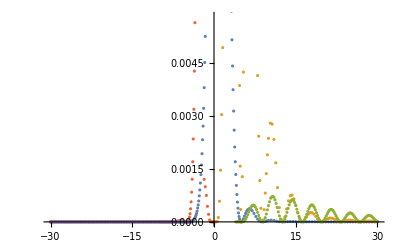

```mathematica
ListPlot[{normedNtoN,normedNtoNplus2,normedNtoNplus4,normedNtoNminus2,normedNtoNminus4}]
```

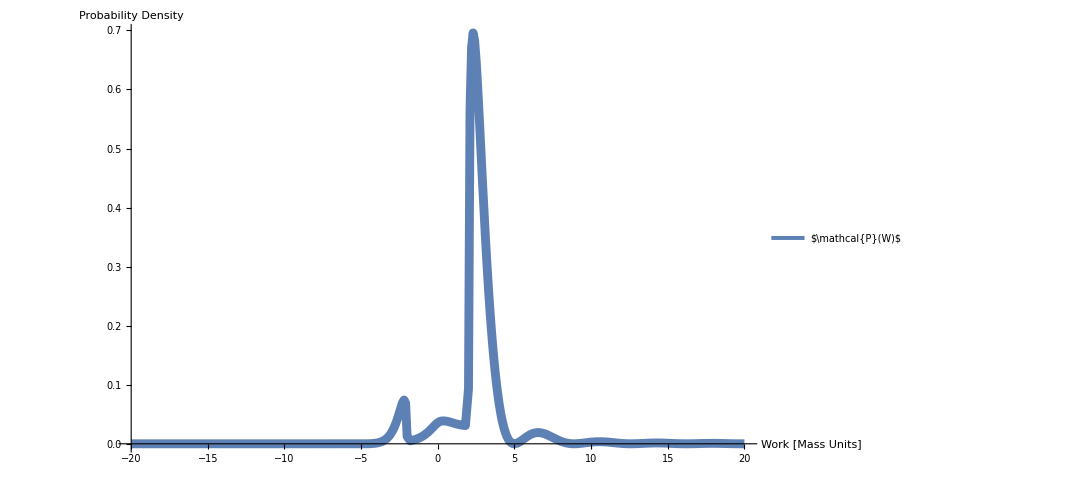

```mathematica
Show[Plot[Piecewise[{{Interpolation[normedNtoNplus4,InterpolationOrder->1][W],4≤W&&W≤30}},0]+Piecewise[{{Interpolation[normedNtoNplus2,InterpolationOrder->1][W],0.001≤W&&W≤30}},0]+Piecewise[{{Interpolation[normedNtoN,InterpolationOrder->1][W],-30≤W&&W≤30}},0]+Piecewise[{{Interpolation[normedNtoNminus2,InterpolationOrder->1][W],-30≤W&&W≤-0.001}},0]+Piecewise[{{Interpolation[normedNtoNminus4,InterpolationOrder->1][W],-30≤W&&W≤-4}},0],{W,-20,20},PlotRange->All,PlotStyle->Directive[Thickness[.008]],AxesStyle->Thickness[.003],TicksStyle->Directive[Thickness[.004], 12],AxesLabel->{Style["Work \n [Mass Units]",Medium],Style["Probability Density",Medium]},TicksStyle->Directive[Medium],PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->Placed[{Style["$\\mathcal{P}(W)$",Medium]},{Right,Center}],AxesOrigin->{-20,0},PlotPoints->200],ImageSize->800]
```

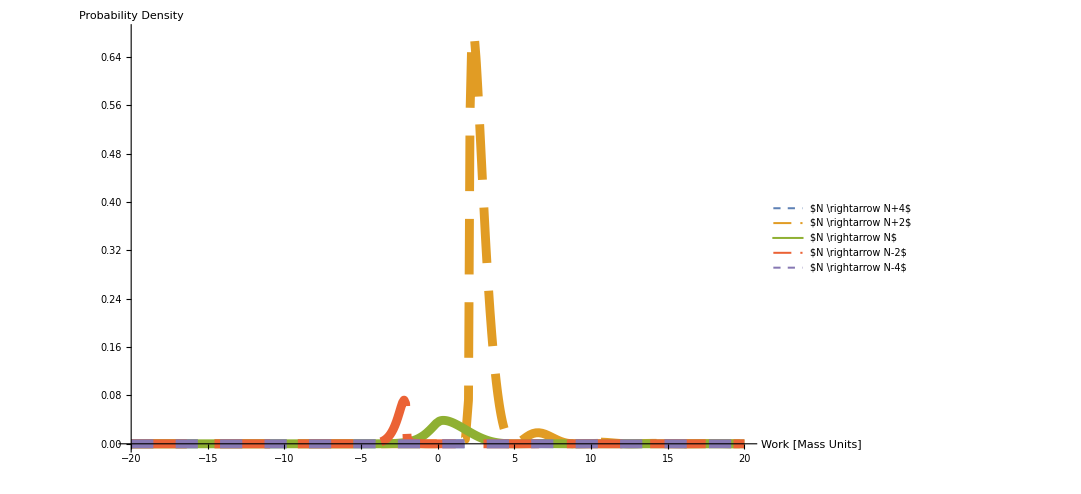

```mathematica
Show[Plot[{Piecewise[{{Interpolation[normedNtoNplus4,InterpolationOrder->1][W],4≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoNplus2,InterpolationOrder->1][W],0.001≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoN,InterpolationOrder->1][W],-30≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoNminus2,InterpolationOrder->1][W],-30≤W&&W≤-0.001}},0],Piecewise[{{Interpolation[normedNtoNminus4,InterpolationOrder->1][W],-30≤W&&W≤-4}},0]},{W,-20,20},PlotRange->All,PlotStyle->{Directive[Dashing[{.02,.02}],Thickness[.008]],Directive[Dashing[{.05,.025}],Thickness[.008]],Directive[Thickness[.008]],Directive[Dashing[{.05,.025}],Thickness[.008]],Directive[Dashing[{.02,.02}],Thickness[.008]]},AxesStyle->Thickness[.003],TicksStyle->Directive[Thickness[.004], 12],AxesLabel->{Style["Work \n [Mass Units]",Medium],Style["Probability Density",Medium]},TicksStyle->Directive[Medium],PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->Placed[{Style["$N \\rightarrow N+4$ \n",Medium],Style["$N \\rightarrow N+2$ \n",Medium],Style["$N \\rightarrow N$ \n",Medium],Style["$N \\rightarrow N-2$ \n",Medium],Style["$N \\rightarrow N-4$ \n",Medium]},{Right,Center}],AxesOrigin->{-20,0},PlotPoints->200],ImageSize->800]
```

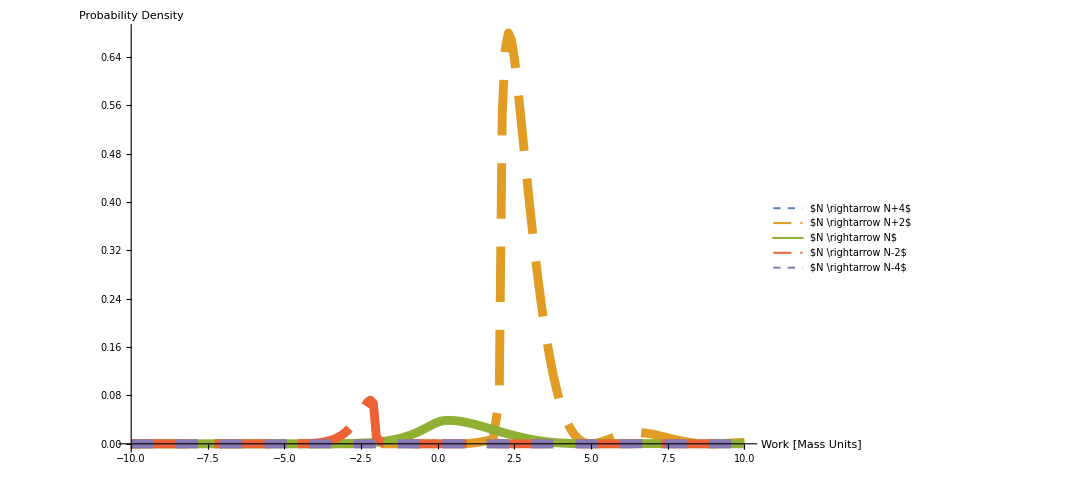

```mathematica
Show[Plot[{Piecewise[{{Interpolation[normedNtoNplus4,InterpolationOrder->1][W],4≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoNplus2,InterpolationOrder->1][W],0.001≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoN,InterpolationOrder->1][W],-30≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoNminus2,InterpolationOrder->1][W],-30≤W&&W≤-0.001}},0],Piecewise[{{Interpolation[normedNtoNminus4,InterpolationOrder->1][W],-30≤W&&W≤-4}},0]},{W,-10,10},PlotRange->All,PlotStyle->{Directive[Dashing[{.02,.02}],Thickness[.008]],Directive[Dashing[{.05,.025}],Thickness[.008]],Directive[Thickness[.008]],Directive[Dashing[{.05,.025}],Thickness[.008]],Directive[Dashing[{.02,.02}],Thickness[.008]]},AxesStyle->Thickness[.003],TicksStyle->Directive[Thickness[.004], 12],AxesLabel->{Style["Work \n [Mass Units]",Medium],Style["Probability Density",Medium]},TicksStyle->Directive[Medium],PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->Placed[{Style["$N \\rightarrow N+4$ \n",Medium],Style["$N \\rightarrow N+2$ \n",Medium],Style["$N \\rightarrow N$ \n",Medium],Style["$N \\rightarrow N-2$ \n",Medium],Style["$N \\rightarrow N-4$ \n",Medium]},{Right,Center}],AxesOrigin->{-10,0},PlotPoints->200],ImageSize->800]
```

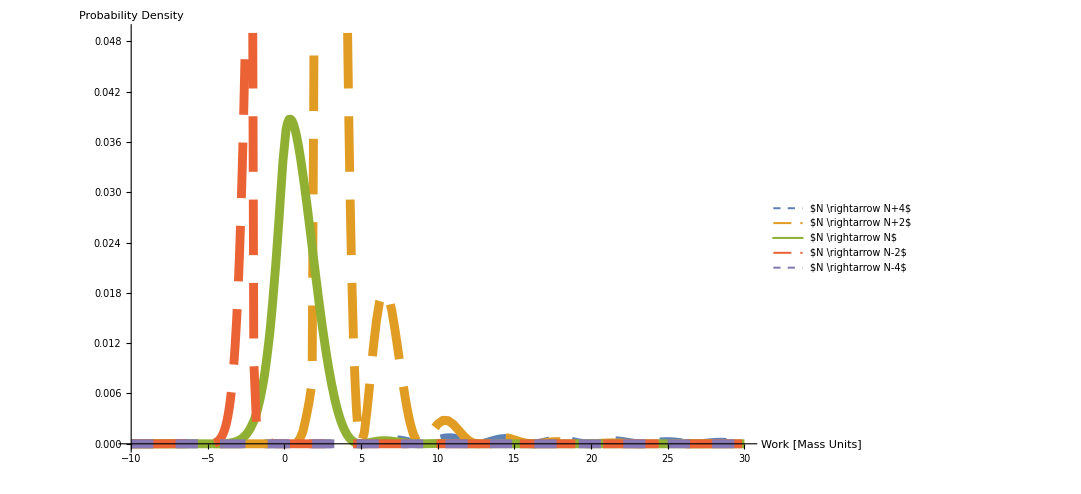

```mathematica
Show[Plot[{Piecewise[{{Interpolation[normedNtoNplus4,InterpolationOrder->1][W],4≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoNplus2,InterpolationOrder->1][W],0.001≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoN,InterpolationOrder->1][W],-30≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoNminus2,InterpolationOrder->1][W],-30≤W&&W≤-0.001}},0],Piecewise[{{Interpolation[normedNtoNminus4,InterpolationOrder->1][W],-30≤W&&W≤-4}},0]},{W,-10,30},PlotRange->{0,.049},PlotStyle->{Directive[Dashing[{.02,.02}],Thickness[.008]],Directive[Dashing[{.05,.025}],Thickness[.008]],Directive[Thickness[.008]],Directive[Dashing[{.05,.025}],Thickness[.008]],Directive[Dashing[{.02,.02}],Thickness[.008]]},AxesStyle->Thickness[.003],TicksStyle->Directive[Thickness[.004], 12],AxesLabel->{Style["Work \n [Mass Units]",Medium],Style["Probability Density",Medium]},TicksStyle->Directive[Medium],PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->Placed[{Style["$N \\rightarrow N+4$ \n",Medium],Style["$N \\rightarrow N+2$ \n",Medium],Style["$N \\rightarrow N$ \n",Medium],Style["$N \\rightarrow N-2$ \n",Medium],Style["$N \\rightarrow N-4$ \n",Medium]},{Right,Center}],AxesOrigin->{-10,0},PlotPoints->200],ImageSize->800]
```

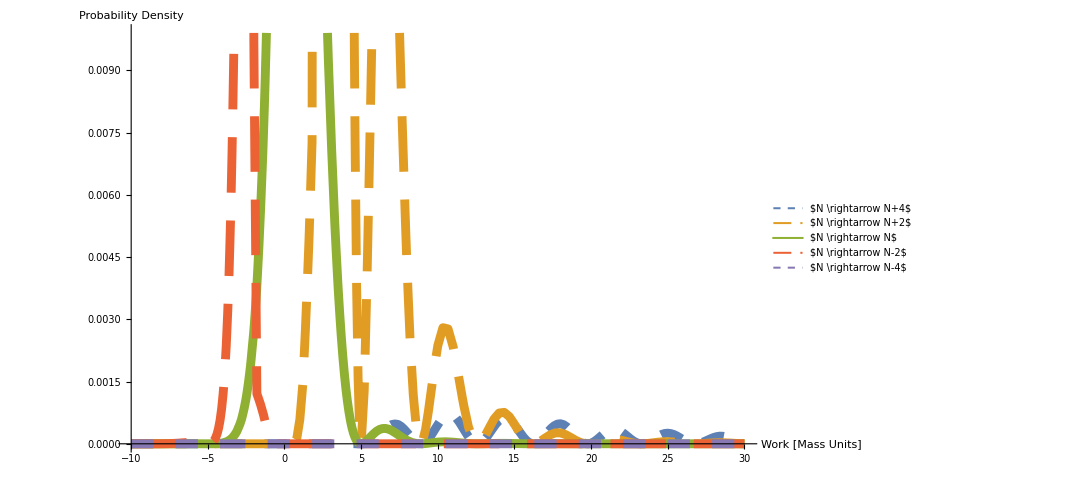

```mathematica
Show[Plot[{Piecewise[{{Interpolation[normedNtoNplus4,InterpolationOrder->1][W],4≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoNplus2,InterpolationOrder->1][W],0.001≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoN,InterpolationOrder->1][W],-30≤W&&W≤30}},0],Piecewise[{{Interpolation[normedNtoNminus2,InterpolationOrder->1][W],-30≤W&&W≤-0.001}},0],Piecewise[{{Interpolation[normedNtoNminus4,InterpolationOrder->1][W],-30≤W&&W≤-4}},0]},{W,-10,30},PlotRange->{0,.0099},PlotStyle->{Directive[Dashing[{.02,.02}],Thickness[.008]],Directive[Dashing[{.05,.025}],Thickness[.008]],Directive[Thickness[.008]],Directive[Dashing[{.05,.025}],Thickness[.008]],Directive[Dashing[{.02,.02}],Thickness[.008]]},AxesStyle->Thickness[.003],TicksStyle->Directive[Thickness[.004], 12],AxesLabel->{Style["Work \n [Mass Units]",Medium],Style["Probability Density",Medium]},TicksStyle->Directive[Medium],PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->Placed[{Style["$N \\rightarrow N+4$ \n",Medium],Style["$N \\rightarrow N+2$ \n",Medium],Style["$N \\rightarrow N$ \n",Medium],Style["$N \\rightarrow N-2$ \n",Medium],Style["$N \\rightarrow N-4$ \n",Medium]},{Right,Center}],AxesOrigin->{-10,0},PlotPoints->200],ImageSize->800]
```

Create exponentially weighted work distribution functions.

```mathematica
weightedNtoN=Table[0,{i,Length[normedNtoN]},{j,2}];Do[weightedNtoN[[i,1]]=normedNtoN[[i,1]];weightedNtoN[[i,2]]=Exp[-normedNtoN[[i,1]]]normedNtoN[[i,2]];,{i,Length[normedNtoN]}]
```

```mathematica
weightedNtoNplus4=Table[0,{i,Length[normedNtoNplus4]},{j,2}];Do[weightedNtoNplus4[[i,1]]=normedNtoNplus4[[i,1]];weightedNtoNplus4[[i,2]]=Exp[-normedNtoNplus4[[i,1]]]normedNtoNplus4[[i,2]];,{i,Length[normedNtoNplus4]}]
```

```mathematica
weightedNtoNplus2=Table[0,{i,Length[normedNtoNplus2]},{j,2}];Do[weightedNtoNplus2[[i,1]]=normedNtoNplus2[[i,1]];weightedNtoNplus2[[i,2]]=Exp[-normedNtoNplus2[[i,1]]]normedNtoNplus2[[i,2]];,{i,Length[normedNtoNplus2]}]
```

```mathematica
weightedNtoNminus4=Table[0,{i,Length[normedNtoNminus4]},{j,2}];Do[weightedNtoNminus4[[i,1]]=normedNtoNminus4[[i,1]];weightedNtoNminus4[[i,2]]=Exp[-normedNtoNminus4[[i,1]]]normedNtoNminus4[[i,2]];,{i,Length[normedNtoNminus4]}]
```

```mathematica
weightedNtoNminus2=Table[0,{i,Length[normedNtoNminus2]},{j,2}];Do[weightedNtoNminus2[[i,1]]=normedNtoNminus2[[i,1]];weightedNtoNminus2[[i,2]]=Exp[-normedNtoNminus2[[i,1]]]normedNtoNminus2[[i,2]];,{i,Length[normedNtoNminus2]}]
```

Numerically verify the Crooks and Jarzynski fluctuation theorems

```mathematica
NIntegrate[Interpolation[normedNtoN,InterpolationOrder->1][W],{W,-30,30}]+
NIntegrate[Interpolation[normedNtoNplus2,InterpolationOrder->1][W],{W,0.001,30}]+
NIntegrate[Interpolation[normedNtoNplus4,InterpolationOrder->1][W],{W,4.001,30}]+
NIntegrate[Interpolation[normedNtoNminus2,InterpolationOrder->1][W],{W,-30,-.001}]+
NIntegrate[Interpolation[normedNtoNminus4,InterpolationOrder->1][W],{W,-30,-4.001}]
```

1.

```mathematica
NIntegrate[Interpolation[weightedNtoN,InterpolationOrder->1][W],{W,-30,30}]/NIntegrate[Interpolation[normedNtoN,InterpolationOrder->1][W],{W,-30,30}]
```

0.994474

```mathematica
NIntegrate[Interpolation[weightedNtoNplus4,InterpolationOrder->1][W],{W,4.001,30}]/
NIntegrate[Interpolation[normedNtoNminus4,InterpolationOrder->1][W],{W,-30,-4.001}]
```

0.999996

```mathematica
NIntegrate[Interpolation[weightedNtoNminus4,InterpolationOrder->1][W],{W,-30,-4.001}]/
NIntegrate[Interpolation[normedNtoNplus4,InterpolationOrder->1][W],{W,4.001,30}]
```

1.

```mathematica
NIntegrate[Interpolation[weightedNtoNminus2,InterpolationOrder->1][W],{W,-30,-.001}]/
NIntegrate[Interpolation[normedNtoNplus2,InterpolationOrder->1][W],{W,.001,30}]
```

1.

```mathematica
NIntegrate[Interpolation[weightedNtoNplus2,InterpolationOrder->1][W],{W,.001,30}]/
NIntegrate[Interpolation[normedNtoNminus2,InterpolationOrder->1][W],{W,-30,-.001}]
```

1.

```mathematica
NIntegrate[Interpolation[weightedNtoN,InterpolationOrder->1][W],{W,-30,30}]+
NIntegrate[Interpolation[weightedNtoNplus2,InterpolationOrder->1][W],{W,0.001,30}]+
NIntegrate[Interpolation[weightedNtoNplus4,InterpolationOrder->1][W],{W,4.001,30}]+
NIntegrate[Interpolation[weightedNtoNminus2,InterpolationOrder->1][W],{W,-30,-.001}]+
NIntegrate[Interpolation[weightedNtoNminus4,InterpolationOrder->1][W],{W,-30,-4.001}]
```

0.999359

Plot work distribution functions by their contribution to the Jarzynski equality.

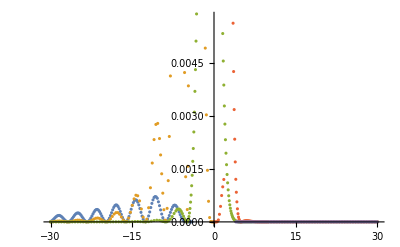

```mathematica
ListPlot[{weightedNtoNminus4,weightedNtoNminus2,weightedNtoN,weightedNtoNplus2,weightedNtoNplus4}]
```

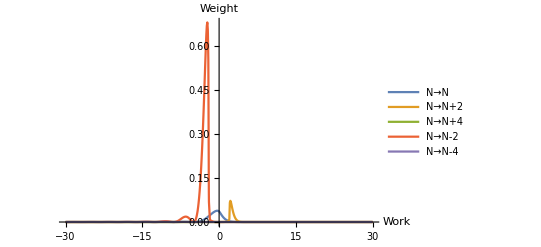

```mathematica
Plot[{Piecewise[{{Interpolation[weightedNtoN,InterpolationOrder->1][W],-30≤W&&W≤30}}],Piecewise[{{Interpolation[weightedNtoNplus2,InterpolationOrder->1][W],0.5≤W&&W≤30}},0],Piecewise[{{Interpolation[weightedNtoNplus4,InterpolationOrder->1][W],4≤W&&W≤30}},0],Piecewise[{{Interpolation[weightedNtoNminus2,InterpolationOrder->1][W],-30≤W&&W≤-0.5}},0],Piecewise[{{Interpolation[weightedNtoNminus4,InterpolationOrder->1][W],-30≤W&&W≤-4}},0]},{W,-30,30},PlotRange->All,AxesLabel->{Style["Work",Large],Style["Weight",Large]},TicksStyle->Directive[Large],PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->{Style["N→N",Large],Style["N→N+2",Large],Style["N→N+4",Large],Style["N→N-2",Large],Style["N→N-4",Large]}]
```

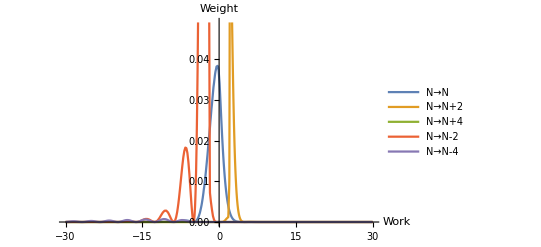

```mathematica
Plot[{Piecewise[{{Interpolation[weightedNtoN,InterpolationOrder->1][W],-30≤W&&W≤30}}],Piecewise[{{Interpolation[weightedNtoNplus2,InterpolationOrder->1][W],0.5≤W&&W≤30}},0],Piecewise[{{Interpolation[weightedNtoNplus4,InterpolationOrder->1][W],4≤W&&W≤30}},0],Piecewise[{{Interpolation[weightedNtoNminus2,InterpolationOrder->1][W],-30≤W&&W≤-0.5}},0],Piecewise[{{Interpolation[weightedNtoNminus4,InterpolationOrder->1][W],-30≤W&&W≤-4}},0]},{W,-30,30},PlotRange->{0,.049},AxesLabel->{Style["Work",Large],Style["Weight",Large]},TicksStyle->Directive[Large],PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->{Style["N→N",Large],Style["N→N+2",Large],Style["N→N+4",Large],Style["N→N-2",Large],Style["N→N-4",Large]}]
```

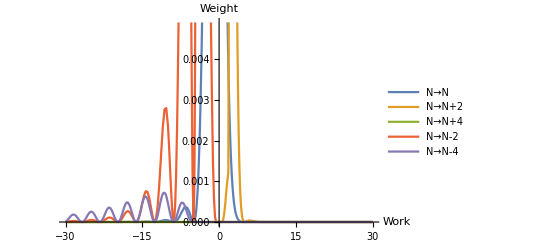

```mathematica
Plot[{Piecewise[{{Interpolation[weightedNtoN,InterpolationOrder->1][W],-30≤W&&W≤30}}],Piecewise[{{Interpolation[weightedNtoNplus2,InterpolationOrder->1][W],0.5≤W&&W≤30}},0],Piecewise[{{Interpolation[weightedNtoNplus4,InterpolationOrder->1][W],4≤W&&W≤30}},0],Piecewise[{{Interpolation[weightedNtoNminus2,InterpolationOrder->1][W],-30≤W&&W≤-0.5}},0],Piecewise[{{Interpolation[weightedNtoNminus4,InterpolationOrder->1][W],-30≤W&&W≤-4}},0]},{W,-30,30},PlotRange->{0,.0049},AxesLabel->{Style["Work",Large],Style["Weight",Large]},TicksStyle->Directive[Large],PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->{Style["N→N",Large],Style["N→N+2",Large],Style["N→N+4",Large],Style["N→N-2",Large],Style["N→N-4",Large]}]
```

```mathematica
interpNtoNm2Total=Interpolation[normedNtoNminus2,InterpolationOrder->1];
```

```mathematica
interpNtoNm2Loop=Interpolation[normedNtoNminus2loop,InterpolationOrder->1];
```

```mathematica
interpNtoNp2Total=Interpolation[normedNtoNplus2,InterpolationOrder->1];
```

```mathematica
interpNtoNp2Loop=Interpolation[normedNtoNplus2loop,InterpolationOrder->1];
```

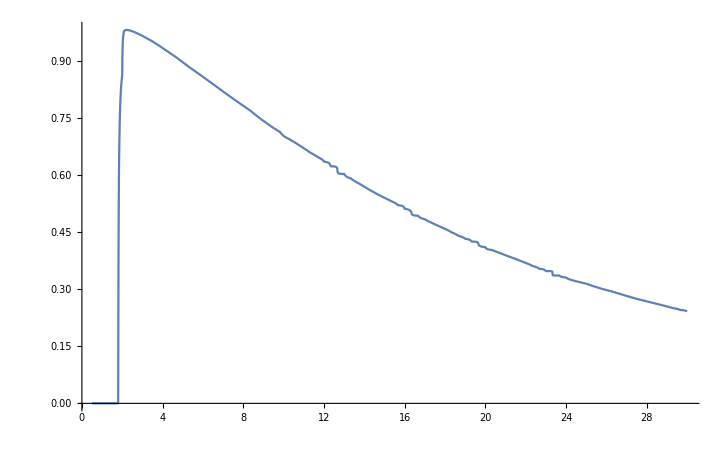

```mathematica
Plot[interpNtoNp2Loop[W]/interpNtoNp2Total[W],{W,.5,30}]
```

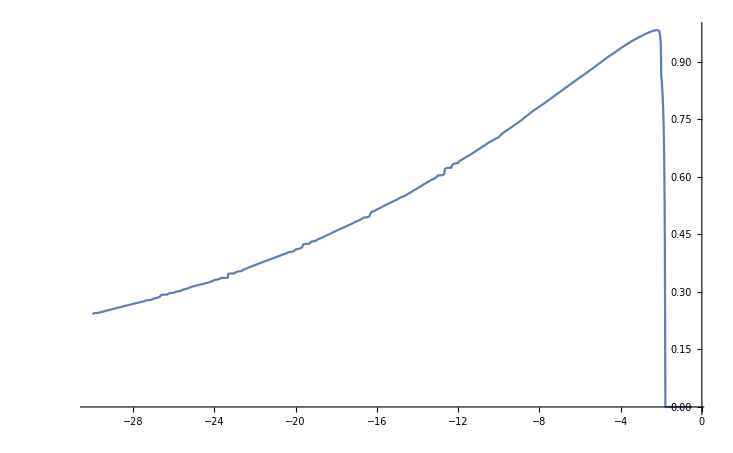

```mathematica
Plot[interpNtoNm2Loop[W]/interpNtoNm2Total[W],{W,-30,-.5}]
```

```mathematica
NIntegrate[interpNtoNp2Loop[W],{W,.001,30}]/NIntegrate[interpNtoNp2Total[W],{W,.001,30}]
```

0.955562

```mathematica
NIntegrate[interpNtoNm2Loop[W],{W,-30,-.001}]/NIntegrate[interpNtoNm2Total[W],{W,-30,-.001}]
```

0.95918

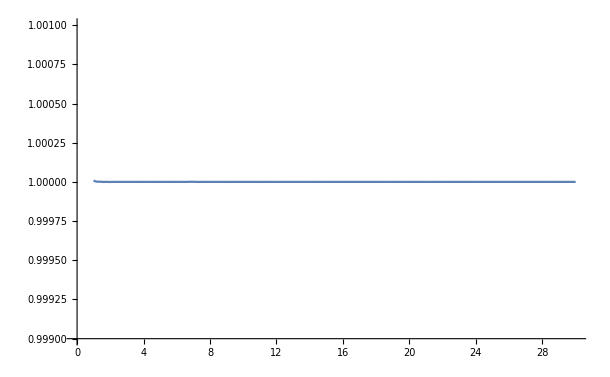

```mathematica
Plot[Interpolation[normedNtoNplus2,InterpolationOrder->1][W]/Interpolation[weightedNtoNminus2,InterpolationOrder->1][-W],{W,1,30},PlotRange->{.999,1.001}]
```

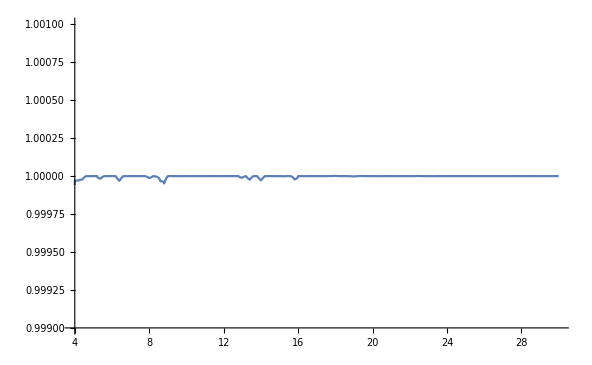

```mathematica
Plot[Interpolation[normedNtoNplus4,InterpolationOrder->1][W]/Interpolation[weightedNtoNminus4,InterpolationOrder->1][-W],{W,4.001,30},PlotRange->{.999,1.001}]
```

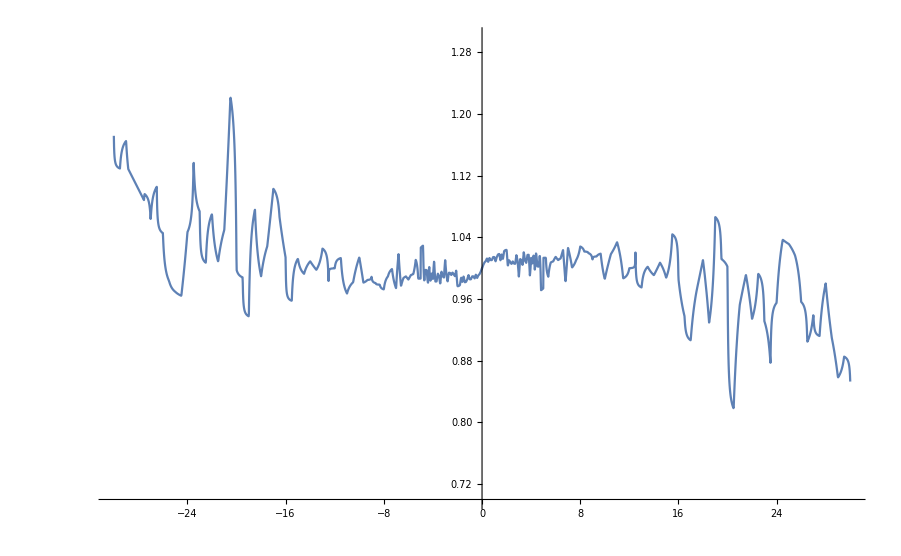

```mathematica
Plot[Interpolation[normedNtoN,InterpolationOrder->1][W]/Interpolation[weightedNtoN,InterpolationOrder->1][-W],{W,-30,30},PlotRange->{.7,1.3}]
```